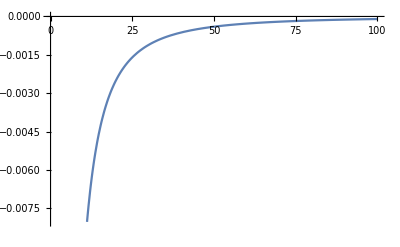

```mathematica
func1[x] := -1/x^2;
func2[x,y]:= func1[x]- Sin[x] + Cos[y^2];

coordArray := ParallelTable[func2[x, y], {x, 1, 10, 1}, {y, -10, -1, 1}];

graf1 = Plot[func1[x], {x, 0, 100}]
```

```mathematica
graf2 = Plot3D[func2[x, y], {x, 0, 100}, {y, -10, 10}]
```

-Graphics3D-

```mathematica
graf3 = ListPlot3D[coordArray]
```

-Graphics3D-

```mathematica
grafArray1 = Table[Plot3D[ func2[x,y]/a^2, {x, -75, 15}, {y, -15, 5}], {a, 1, 3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
slide = SlideView[grafArray1]
```

```mathematica
grafArray2 = Table[Plot3D[ func2[x,y]/ (x + y), {x, -75, 15}, {y, -15, 5}], 1]
```

{-Graphics3D-}

{-Graphics3D-}

```mathematica
Export ["D:\\Wolfram\\Projects\\GrafSlideView.gif", grafArray]
Export ["D:\\Wolfram\\Projects\\Function.dat", grafArray2]
func = Import["D:\\Wolfram\\Projects\\Function.dat"]
Plot3D[func, {x, 1, 10}, {y, 1, 10}, {a, 1, 3}]
```

D:\Wolfram\Projects\GrafSlideView.gif

D:\Wolfram\Projects\Function.dat

{{Graphics3D[GraphicsComplex[{{-74.99999357142858,,-14.999998571428572,,-0.020685832567776674},,{-68.5714230612245,,-14.999998571428572,,-0.15016668176913656},,{-62.14285255102041,,-14.999998571428572,,-0.26874546488092516},,{-55.71428204081633,,-14.999998571428572,,-0.3739267337510374},,{-49.28571153061225,,-14.999998571428572,,-0.4635019218585876},,{-42.857141020408164,,73211,{{-75,,15},,{-15,,5},,{-4.453174370024782,,1.9955899886598538}},,PlotRangePadding,->,{Scaled[0.02],,Scaled[0.02],,Scaled[0.02]},,Ticks,->,{Automatic,,Automatic,,Automatic}}]},{1},{1}}
 |  |  |  |

Plot3D::nonopt: Options expected (instead of {a,1,3}) beyond position 3 in Plot3D[func,{x,1,10},{y,1,10},{a,1,3}]. An option must be a rule or a list of rules.

Plot3D[func,{x,1,10},{y,1,10},{a,1,3}]